```mathematica
avogadroConstant=6.02214086*10^23;
oneOverGevToCm=0.197*10^-13;(*cm*)
cmToKm=10^-5;
evToGeV=10^-9;
values={
ne->2.2*avogadroConstant*oneOverGevToCm^3,(*GeV^3*)
gf->1.1663787*10^-5,(*GeV^-2*)
dm221->7.56*10^-5*evToGeV^2,(*GeV^2*)
dm2LargeAbs->2.55*10^-3*evToGeV^2,(*GeV^2*)
(*dm231->2.55*10^-3*evToGeV^2,(*GeV^2*)*)
baseline->810*10^5/oneOverGevToCm,(*GeV^-1*)
theta13->8.41*Degree,
theta12->34.5*Degree
(*theta23->41.*Degree*)
(*delta->252.*Degree*)
};
```

```mathematica
getAppearanceProbability[e_,isNu_,matterEffectScale_,deltaCp_,isNormalOrdering_,th23_]=Module[{isNuSign,a,d21,d31,prob},
isNuSign=If[isNu,1,-1];

(*a=isNuSign*gf*ne/Sqrt[2]*matterEffectScale;*)
a=isNuSign/3500*oneOverGevToCm*cmToKm*matterEffectScale;(*GeV, NunokawaPV08*)

(*dm231=If[isNormalOrdering, 
dm2LargeAbs+dm221/2,
-dm2LargeAbs+dm221/2
];
*)
dm231=If[isNormalOrdering, dm2LargeAbs,-dm2LargeAbs];

d21=dm221/(4*e)*baseline;
d31=dm231/(4*e)*baseline;

prob=Sin[theta23]^2*Sin[2*theta13]^2*Sin[d31-a*baseline]^2/(d31-a*baseline)^2*d31^2
+Cos[theta23]^2*Sin[2*theta12]^2*Sin[a*baseline]^2/(a*baseline)^2*d21^2
+Sin[2*theta23]*Sin[2*theta13]*Sin[2*theta12]*Sin[d31-a*baseline]/(d31-a*baseline)*d31*Sin[a*baseline]/(a*baseline)*d21*Cos[d31+delta*isNuSign];
prob/.values/.delta->deltaCp/.theta23->th23
];
```

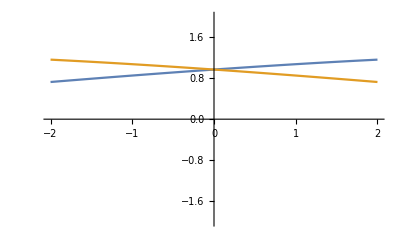

```mathematica
getD31SinxOverX[scale_,isNormalOrdering_]:=Module[{isNuSign,a,e},
isNuSign=1;
e=2;
a=isNuSign/3500*oneOverGevToCm*cmToKm*scale;
dm231=If[isNormalOrdering, dm2LargeAbs,-dm2LargeAbs];
d31=dm231/(4*e)*baseline;
Abs[d31*Sin[d31-a*baseline]/(d31-a*baseline)/.values]
];

Plot[{
getD31SinxOverX[x,True],
getD31SinxOverX[x,False]
},{x,-2,2},
PlotRange->{{-2,2},{-2,2}}
]
```

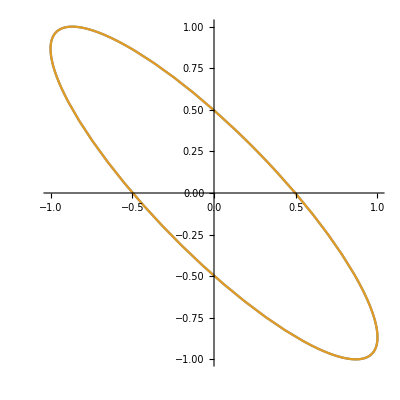

```mathematica
e=2;
d31=dm2LargeAbs/(4*e)*baseline/.values;
ParametricPlot[{
{Cos[x+d31],Cos[-x+d31]},
{Cos[x-d31],Cos[-x-d31]}
},
{x,0,2*Pi}
]
Clear[e,d31]
```

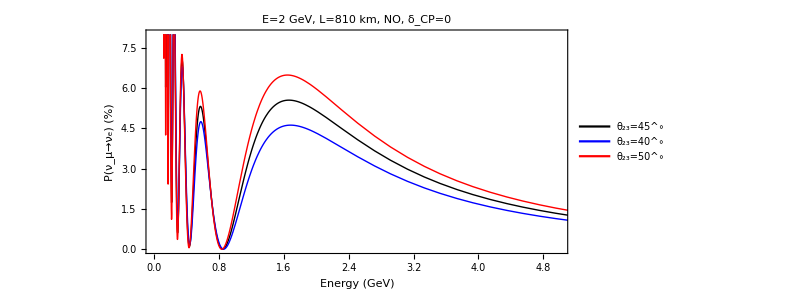

/Users/juntinghuang/beamer/20180218_ustc_minos_nova/figures/neutrino/theta23_octant.pdf

```mathematica
(*compare theta23 octant*)
plot=Plot[{
getAppearanceProbability[x,True,1,0,True,45.*Degree]*100,
getAppearanceProbability[x,True,1,0,True,40.*Degree]*100,
getAppearanceProbability[x,True,1,0,True,50.*Degree]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[Automatic,{"θ_23=45^∘","θ_23=40^∘","θ_23=50^∘"},LegendMarkerSize->20],{0.8,0.6}],
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Red,Thick]},
PlotRange->{{0,5},{0,8}},
ImageSize->600,
AspectRatio->0.5,
BaseStyle->{FontSize->30},
Frame->True,
FrameLabel->{{"P(ν_μ→ν_e) (%)",None},{"Energy (GeV)",None}},
FrameStyle->Directive[Black,Thick],
PlotLabel->Style["E=2 GeV, L=810 km, NO, δ_CP=0",FontSize->30]
]
Export["/Users/juntinghuang/beamer/20180218_ustc_minos_nova/figures/neutrino/theta23_octant.pdf",plot]
```

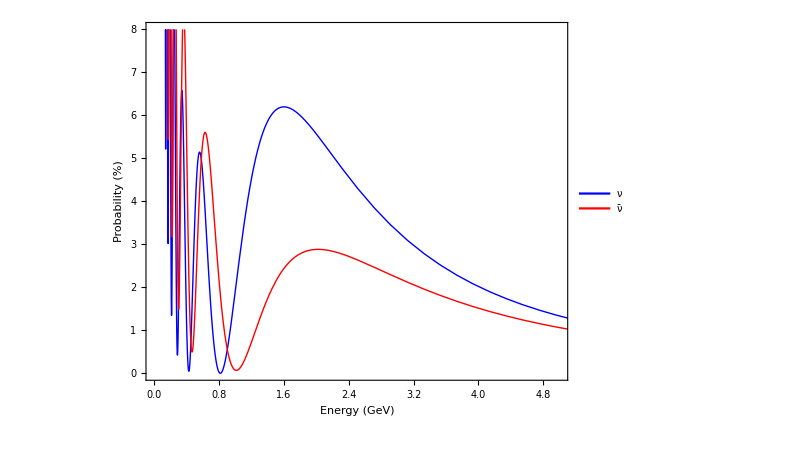

```mathematica
plot=Plot[{
getAppearanceProbability[x,True,1,0,True,45.*Degree]*100,
getAppearanceProbability[x,True,1,0,True,45.*Degree]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[{"ν","ν̄"},LegendMarkerSize->40],{0.75,0.75}],
PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},
PlotRange->{{0,5},{0,8}},
ImageSize->600,
AspectRatio->600/800,
BaseStyle->{FontSize->20},
Frame->True,
FrameLabel->{{"Probability (%)",None},{"Energy (GeV)",None}},
FrameStyle->Directive[Black,Thick]
]
```

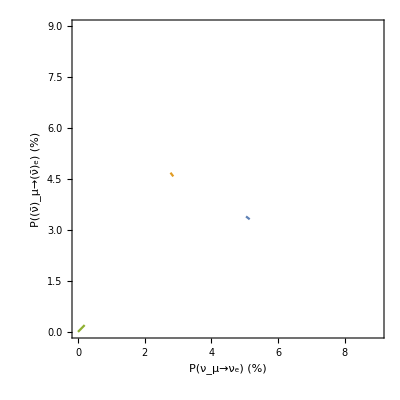

```mathematica
matterEffectScalingFactor=1;
biprob=ParametricPlot[{
{getAppearanceProbability[2,True,matterEffectScalingFactor,x,True,45.*Degree]*100,getAppearanceProbability[2,False,matterEffectScalingFactor,x,True,45.*Degree]*100},
{getAppearanceProbability[2,True,matterEffectScalingFactor,x,False,45.*Degree]*100,getAppearanceProbability[2,False,matterEffectScalingFactor,x,False,45.*Degree]*100},
{x*2,x*2}
},
(*{x,0,2*Pi},*)
{x,0,0.1},
PlotRange->{{0,9},{0,9}},
ImageSize->400,
AspectRatio->1,
Frame->True,
FrameLabel->{{"P((ν̄)_μ→(ν̄)_e) (%)",None},{"P(ν_μ→ν_e) (%)",None}},
FrameStyle->Directive[Black,Thick],
BaseStyle->{FontSize->20}
]
```

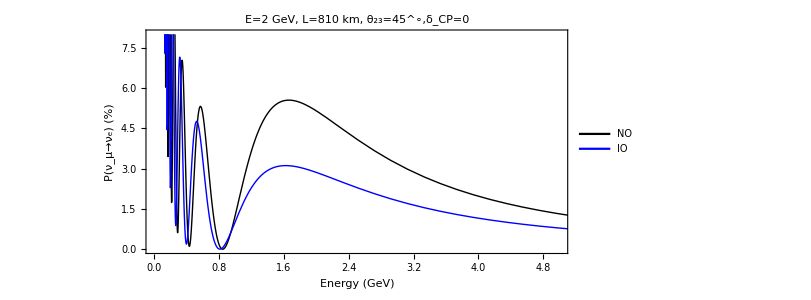

/Users/juntinghuang/beamer/20180218_ustc_minos_nova/figures/no_vs_io.pdf

```mathematica
(*plot effect of mass ordering*)
plot=Plot[{
getAppearanceProbability[x,True,1,0,True,45.*Degree]*100,
getAppearanceProbability[x,True,1,0,False,45.*Degree]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[{"NO","IO"},LegendMarkerSize->40],{0.8,0.7}],
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick]},
PlotRange->{{0,5},{0,8}},
ImageSize->600,
AspectRatio->0.5,
BaseStyle->{FontSize->30},
Frame->True,
FrameLabel->{{"P(ν_μ→ν_e) (%)",None},{"Energy (GeV)",None}},
FrameStyle->Directive[Black,Thick],
PlotLabel->Style["E=2 GeV, L=810 km, θ_23=45^∘,δ_CP=0",FontSize->30]
];
text=Graphics[{Text["Left Aligned",{3,3},{-1,0}]}];
Show[plot]
Export["/Users/juntinghuang/beamer/20180218_ustc_minos_nova/figures/no_vs_io.pdf",plot]
```

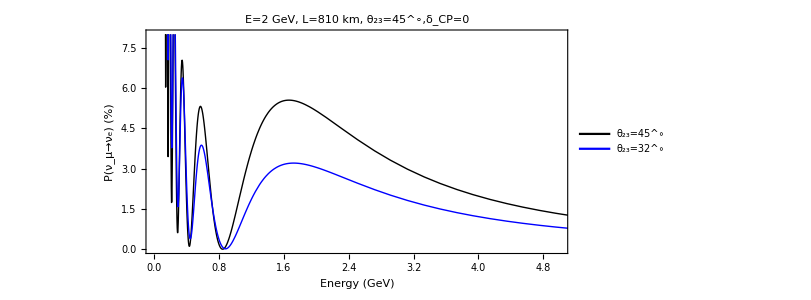

/Users/juntinghuang/beamer/20180218_ustc_minos_nova/figures/neutrino/theta23_octant.pdf

```mathematica
plot=Plot[{
getAppearanceProbability[x,True,1,0,True,45.*Degree]*100,
getAppearanceProbability[x,True,1,0,True,32.*Degree]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[{"θ_23=45^∘","θ_23=32^∘"},LegendMarkerSize->40],{0.8,0.7}],
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick]},
PlotRange->{{0,5},{0,8}},
ImageSize->600,
AspectRatio->0.5,
BaseStyle->{FontSize->30},
Frame->True,
FrameLabel->{{"P(ν_μ→ν_e) (%)",None},{"Energy (GeV)",None}},
FrameStyle->Directive[Black,Thick],
PlotLabel->Style["E=2 GeV, L=810 km, θ_23=45^∘,δ_CP=0",FontSize->30]
];
Show[plot]
Export["/Users/juntinghuang/beamer/20180218_ustc_minos_nova/figures/neutrino/theta23_octant.pdf",plot]
```